# Import data

This will open a window  to select the CSV file with the data.

```mathematica
(*Open file selector dialog*)
fileDialogResult=SystemDialogInput["FileOpen","*.csv"];
data=Import[fileDialogResult,"CSV","SkipLines"->1];
data=Select[data,Length[#]==4&];(*In about 20% of the files there are errors. This removes damaged lines*)
```

## Extract data, set sample rate

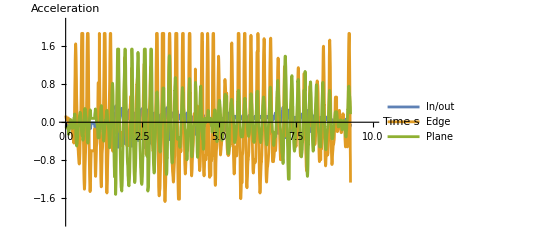

```mathematica
fs=250;(*SampleRate of the Pico device*)
timestepDiv=1000;(*Ticks since reboot in milliseconds - so we need to divide*)
tims=(data[[All,1]]-data[[1,1]])/timestepDiv;(*Take the first column and set the first sample at time zero*)
tims=MedianFilter[tims,3];(*Sometimes the Pico throws in an errant timestamp value. This filters outliers*)

(*Extract x,y,z data and substract the mean for each*)
{x,y,z}=Transpose[data[[All,2;;4]]];
x=x//._String->0;
y=y//._String->0;
z=z//._String->0;

x=#-Mean[x]&/@x;
y=#-Mean[y]&/@y;
z=#-Mean[z]&/@z;

Xdata=TimeSeriesResample[Transpose[{tims,x}],1/fs];(*Forward direction Blue*)
Ydata=TimeSeriesResample[Transpose[{tims,y}],1/fs];(*Side direction Orange*)
Zdata=TimeSeriesResample[Transpose[{tims,z}],1/fs];(*Planar direction Green*)
ListLinePlot[{Xdata,Ydata,Zdata},PlotRange->{{0,10},{-2.1,2.1}},AxesLabel->{"Time s","Acceleration"},PlotLegends->{"In/out","Edge","Plane"}]
```

## Highpass filter

```mathematica
hipass=0.1;
x=HighpassFilter[x,2 π hipass/fs];
y=HighpassFilter[y,2 π hipass/fs];
z=HighpassFilter[z,2 π hipass/fs];
```

## Lowpass filter the data and plot again

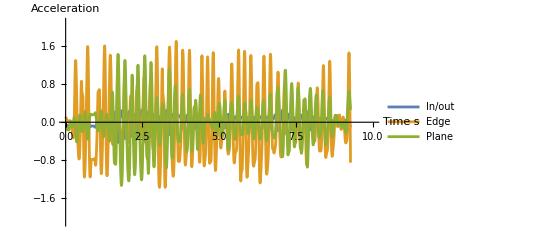

```mathematica
cutoffreq=8;
filtX=LowpassFilter[x,2 π cutoffreq/fs];
filtY=LowpassFilter[y,2 π cutoffreq/fs];
filtZ=LowpassFilter[z,2 π cutoffreq/fs];

ListLinePlot[{Transpose[{tims,filtX}],Transpose[{tims,filtY}],Transpose[{tims,filtZ}]},PlotRange->{{0,10},{-2.1,2.1}},AxesLabel->{"Time s","Acceleration"},PlotLegends->{"In/out","Edge","Plane"}]
```

## Calculate Fourier spectrum and plot

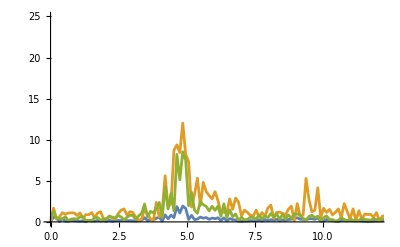

```mathematica
fftX=Abs[Fourier[Xdata[[All,2]]]];
fftY=Abs[Fourier[Ydata[[All,2]]]];
fftZ=Abs[Fourier[Zdata[[All,2]]]];

plotdataX=fftX[[1;;Floor[Length[fftX]/2]+1]];
plotdataY=fftY[[1;;Floor[Length[fftY]/2]+1]];
plotdataZ=fftZ[[1;;Floor[Length[fftZ]/2]+1]];

fftFreqs=N@Subdivide[1/fs,fs/2,Floor[Length[fftZ]/2]];

ListLinePlot[{Transpose[{fftFreqs,plotdataX}],Transpose[{fftFreqs,plotdataY}],Transpose[{fftFreqs,plotdataZ}]},PlotRange->{{0,cutoffreq*1.5},{0,25}}]
```

## Calculate and plot the zero crossing data

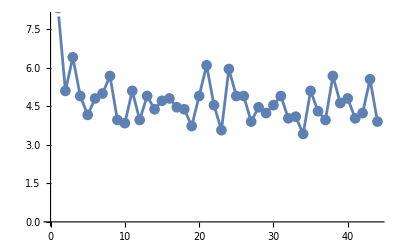

The mean instantaneous frequency is 4.71357 Hz.

```mathematica
positiveZeroCrossings=Flatten@Position[Differences[Sign[filtZ]],2];

(*Calculate instantaneous frequency based on number of samples between consecutive positive zero crossings*)
instFreq=1/(Differences[positiveZeroCrossings]/fs);
ListLinePlot[instFreq,PlotMarkers->Automatic,PlotRange->{Automatic,{0,cutoffreq}}]

Print[StringJoin["The mean instantaneous frequency is ",ToString[N[Mean[instFreq]]]," Hz."]];
```